```mathematica
ClearAll[x,y]
(*Plot[{x^2+ y^2 == 25,x - y == 7},{x,-10,10},{y,-10,10}]*)
```

Plot::nonopt: Options expected (instead of {y,-10,10}) beyond position 2 in Plot[{x^2+y^2==25,x-y==7},{x,-10,10},{y,-10,10}]. An option must be a rule or a list of rules.

Plot[{x^2+y^2==25,x-y==7},{x,-10,10},{y,-10,10}]

```mathematica
Solve[{x^2+ y^2 == 25,x - y == 7},{x,y}]
x y /. Solve[{x^2+ y^2 == 25,x - y == 7},{x,y}]
```

{{x→3,y→-4},{x→4,y→-3}}

{-12,-12}

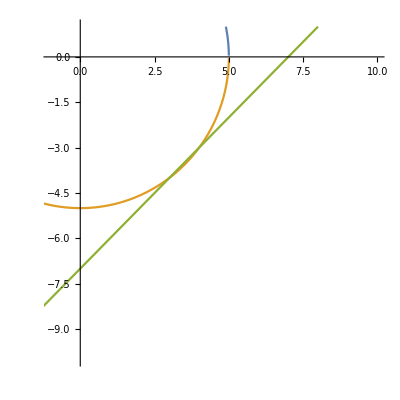

```mathematica
Plot[{Sqrt[25-x^2],-Sqrt[25-x^2],x - 7},{x,-10,10}, AspectRatio->1, PlotRange-> {{-1,10},{-10,1}}]
```